## Walter, Differential Equations. Problem Set, page 24.

### (c) y'=√((1-y) Abs[y]);y≤1

Here is a picture of the vector field. y=0 and y=1 are solutions. We will look for solutions in two regions:
0≤y≤1 andy<0.

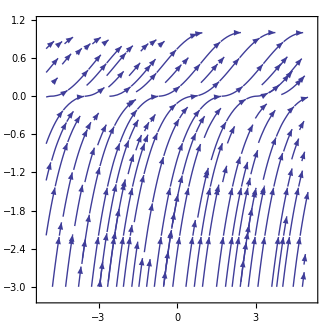
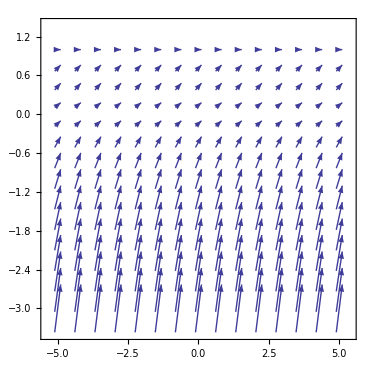

```mathematica
{StreamPlot[{1,Sqrt[(1-y)Abs[y]]},{x,-5,5},{y,-3,1}],VectorPlot[{1,Sqrt[(1-y)Abs[y]]},{x,-5,5},{y,-3,1}]}
```

We will show that the solution is y=1/2 (sin(c+x)+1)for -π/2≤c+x≤π/2 for 0≤y≤1 and
 and y=1/2 (1-cosh(c-x)) for c-x<0 for y<0

```mathematica
Clear[f]
```

```mathematica
f[x_]:=(1/2)(Sin[x]+1)/;-Pi/2≤x≤Pi/2
```

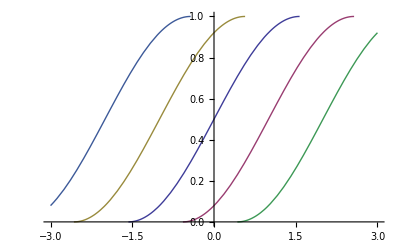

```mathematica
plota=Plot[{f[x],f[x-1],f[x+1], f[x-2],f[x+2]},{x,-3,3},PlotStyle->Thick]
```

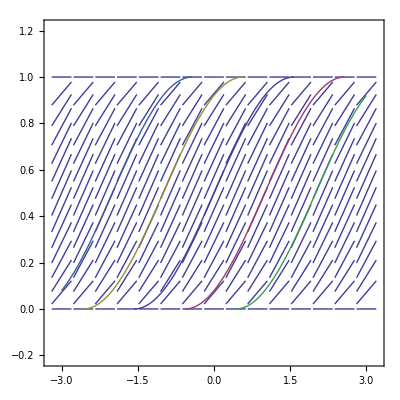

```mathematica
Show[VectorPlot[{1,Sqrt[y(1-y)]},{x,-3,3},{y,0,1},VectorStyle->Arrowheads[0]],plota]
```

```mathematica
Clear[g]
```

```mathematica
g[x_]:=(1/2)(1-Cosh[x])/;x<0
```

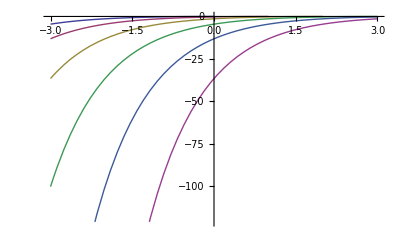

```mathematica
plotb=Plot[{g[x],g[x-1],g[x-2],g[x-3],g[x-4],g[x-5]},{x,-3,3}]
```

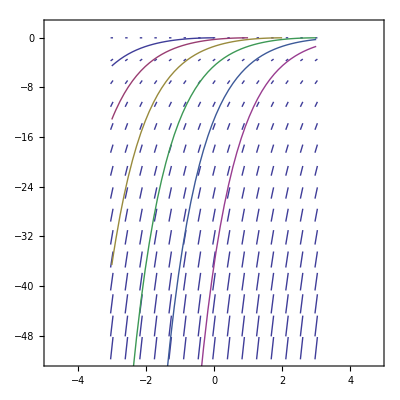

```mathematica
Show[VectorPlot[{1,Sqrt[y^2-y]},{x,-3,3},{y,-50,0},VectorStyle->Arrowheads[0]],plotb]
```

```mathematica
funrestricted[x_]:=(1/2)(Sin[x]+1)
```

```mathematica
D[funrestricted[x],x]
```

Cos[x]/2

```mathematica
Simplify[Sqrt[funrestricted[x](1-funrestricted[x])], -Pi/2<x<Pi/2]
```

Cos[x]/2

```mathematica
gunrestriced[x_]:=(1/2)(1-Cosh[x])
```

```mathematica
D[gunrestriced[x],x]
```

-Sinh[x]/2

```mathematica
Simplify[Sqrt[gunrestriced[x](gunrestriced[x]-1)],x<0]
```

-Sinh[x]/2

Just for fun let’s see if Mathematica can solve it.

```mathematica
eqn:=y'[x]==Sqrt[(1-y[x])Abs[y[x]]];
```

```mathematica
eqn// TraditionalForm
```

y'(x)==√(1-y(x)) √Abs[y(x)]

```mathematica
sol =Assuming[{Element[x,Reals],y[x]<1},DSolve[eqn,y[x],x]]
```

{{y[x]→InverseFunction[-2 ArcCos[√#1] √Sign[#1]&][x+C[1]]}}

For non-negative y this means x=-2 cos^-1(√y) and so y=Cos^2[(-1/2)x]=1/2(cos(x+c)+1)
This solution works for segments of the graph where it is increasing and there it is the same solution we found above.

For negative y we have x=-2 ⅈ cos^-1(√y) or cos((i x)/2)=√y
or cosh(x/2)=√y (See ComplexTrig.nb and Ahlfors pg 47)
or y=cosh^2(x/2)=(1/2)(cosh(x)+1). This solution does not make sense for y<0. Instead it is the solution for y>1.

Let’s ask Mathematica to solve just the non-negative y equation.

```mathematica
eqn1 := y'[x]==Sqrt[y[x]-y[x]^2];
```

```mathematica
eqn1//TraditionalForm
```

y'(x)==√(y(x)-(y(x))^2)

```mathematica
sol1=Assuming[{Element[x,Reals],0<y[x]<1},DSolve[eqn1,y[x],x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→1/4 ⅇ^(-ⅈ x-ⅈ C[1]) (1+ⅇ^(ⅈ x+ⅈ C[1]))^2}}

```mathematica
FullSimplify[y[x]/.sol1[[1]]]
```

Cos[1/2 (x+C[1])]^2

This is the same solution as before.

Now lets ask Mathematica to solve just the non-positive y equation.

```mathematica
eqn2:=y'[x]==Sqrt[y[x]^2-y[x]]
```

```mathematica
eqn2//TraditionalForm
```

y'(x)==√((y(x))^2-y(x))

```mathematica
sol2=Assuming[{Element[x,Reals],y[x]<0},DSolve[eqn2,y[x],x]]
```

{{y[x]→1/4 ⅇ^(-x-C[1]) (1+ⅇ^(x+C[1]))^2}}

```mathematica
FullSimplify[y[x]/.sol2[[1]]]
```

Cosh[1/2 (x+C[1])]^2

This is the same wrong function as above but we are looking for a y[x] that is increasing and  negative. This function solves the differential equation for y>1

```mathematica
h[x_]:=Cosh[1/2 (x)]^2
```

```mathematica
h'[x]//FullSimplify
```

```mathematica
Sinh[x]/2
```

```mathematica
Sqrt[h[x]^2-h[x]]//FullSimplify
```

1/2 √(Sinh[x]^2)

### (d) y'=(e^(-y^2))/(y(x^2+2 x)), y(2)=0

The solution is y=√(log(log(x/(x+2))+(1+log(2))))

```mathematica
fd1[x_,y_]:=Exp[-y^2]/(y(x^2+2x))
```

```mathematica
TraditionalForm[fd1[x,y]]
```

(ⅇ^(-y^2))/((x^2+2 x) y)

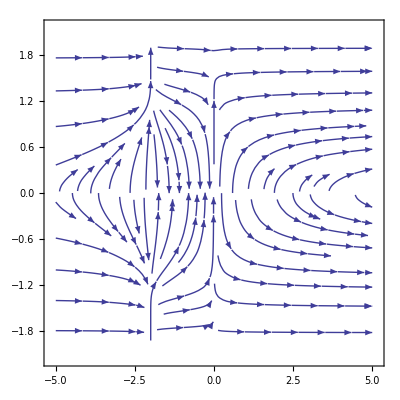

```mathematica
StreamPlot[{1,fd1[x,y]},{x,-5,5},{y,-2,2}]
```

```mathematica
{Integrate[Exp[y^2]y,y],Integrate[1/(x^2+2x),x]}
```

{(ⅇ^(y^2))/2,Log[x]/2-1/2 Log[2+x]}

```mathematica
fd2[x_]:=Sqrt[Log[Log[x/(2+x)]+c]]
```

```mathematica
fd2[x]//TraditionalForm
```

√(log(c+log(x/(x+2))))

```mathematica
fd2'[x]//FullSimplify
```

1/(x (2+x) (c+Log[x]-Log[2+x]) √Log[c+Log[x]-Log[2+x]])

```mathematica
fd1[x,fd2[x]]//FullSimplify
```

1/(x (2+x) (c+Log[x]-Log[2+x]) √Log[c+Log[x]-Log[2+x]])

```mathematica
fd2[2]/.c->(1+Log[2])
```

0

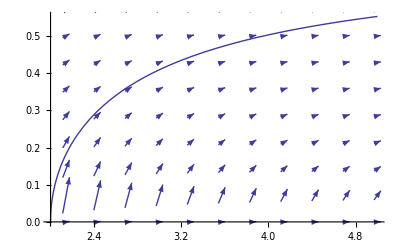

```mathematica
Show[fd2plot,VectorPlot[{1,fd1[x,y]},{x,1,5},{y,0,1}]]
```

### (e) y'=(yLog(y))/(sin(x)), y(π/2)=ⅇ^ⅇ

The solution is y=ⅇ^(ⅇ tan(x/2)). This function is continuous with continuous derivative 1/2 sec^2(x/2) exp(ⅇ tan(x/2)+1) on (-π, π).
It satisfies the differential equation on (0, π). The function passes through the point (0, 1) but it does not satisfy the differential equation
at that point because the value of the slope field at (0,1) tends to 1 but the value of the derivative at 0 is ⅇ/2. The slope field is pathological
on the y-axis because its value tends to infinity everywhere except at y=1.

```mathematica
fe1[x_,y_] :=y*Log[y]/Sin[x]
```

```mathematica
TraditionalForm[fe1[x,y]]
```

y csc(x) log(y)

```mathematica
{N[E^E],fe1[Pi/2,E^E], N[fe1[Pi/2,E^E]], fe1[0.00001,1.00001]}
```

{15.1543,ⅇ^(1+ⅇ),41.1936,1.00001}

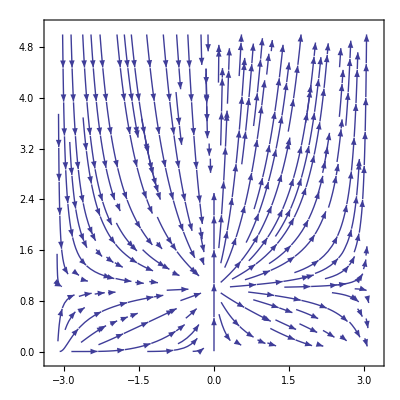

```mathematica
StreamPlot[{1,fe1[x,y]},{x,-Pi,Pi},{y,0,5}]
```

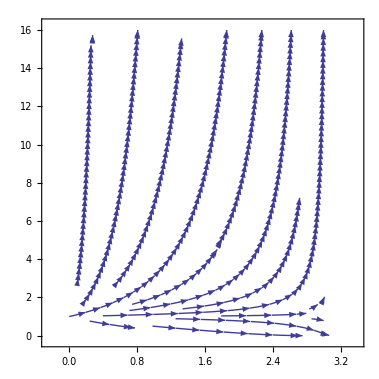

```mathematica
StreamPlot[{1,fe1[x,y]},{x,0,Pi},{y,0,16}]
```

```mathematica
{Integrate[1/(Log[y]y),y],Integrate[Csc[x],x]}
```

{Log[Log[y]],-Log[Cos[x/2]]+Log[Sin[x/2]]}

```mathematica
FullSimplify[D[Log[Tan[x/2]],x]]
```

Csc[x]

```mathematica
fe2[x_]:=Exp[c*Tan[x/2]]
```

```mathematica
fe2[x]//TraditionalForm
```

ⅇ^(c tan(x/2))

```mathematica
fe2[Pi/2]/.c->E
```

ⅇ^ⅇ

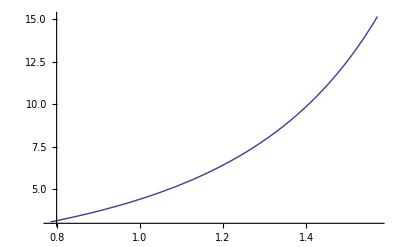

```mathematica
plote = Plot[fe2[x]/.c->E,{x,Pi/4,Pi/2}]
```

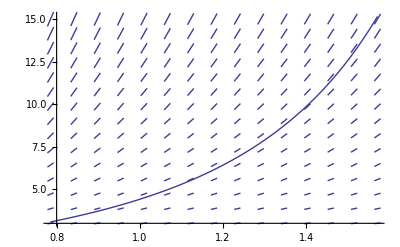

```mathematica
Show[plote,VectorPlot[{1,fe1[x,y]},{x,Pi/4,Pi/2},{y,3,15},VectorStyle->Arrowheads[0]]]
```

```mathematica
fe2'[x]
```

1/2 c ⅇ^(c Tan[x/2]) Sec[x/2]^2

```mathematica
FullSimplify[fe1[x,fe2[x]],Pi/4<x<3Pi/4]
```

ⅇ^(c Tan[x/2]) Csc[x] Log[ⅇ^(c Tan[x/2])]

```mathematica
TrigExpand[FullSimplify[c*ⅇ^(c Tan[x/2]) Csc[x]Tan[x/2]]]
```

1/2 c ⅇ^(c Tan[x/2]) Sec[x/2]^2

```mathematica
fe2'[0]
```

c/2

```mathematica
DSolve[{y'[x]==fe1[x,y[x]]},y[x],x]
```

{{y[x]→ⅇ^(ⅇ^C[1] Tan[x/2])}}

### (g)y'=(x-y+3)^2

The solutions are y=x+2, y=x+4, y=-tanh(c+x)+x+3,  y=-coth(c+x)+x+3

```mathematica
fg1[x_,y_]:=(x-y+3)^2
```

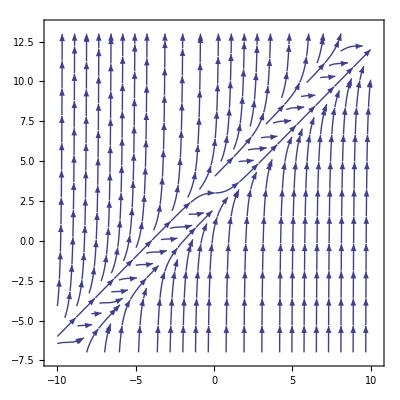

```mathematica
StreamPlot[{1,fg1[x,y]},{x,-10,10},{y,-7,13}]
```

Make the substitution u=x-y. Then u'=1-y'=1-(u+3)^2

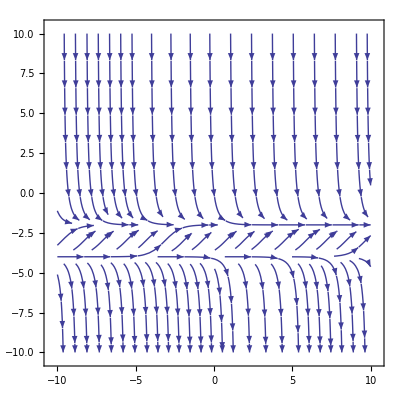

```mathematica
StreamPlot[{1,1-(u+3)^2},{x,-10,10},{u,-10,10}]
```

Then u(x)=-2 and u(x)=-4 are solutions with u'=0. So y(x)=x+2 and y(x)=x+4 are solutions with y'=1.

```mathematica
FullSimplify[Integrate[1/(1-(u+3)^2),u]]
```

ArcTanh[3+u]

```mathematica
{D[ArcTanh[3+u],u],D[ArcCoth[3+u],u]}
```

{1/(1-(3+u)^2),1/(1-(3+u)^2)}

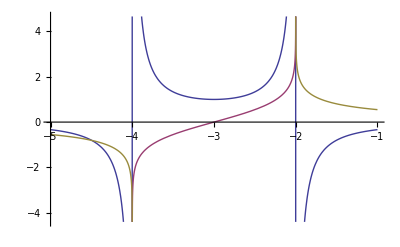

```mathematica
Plot[{1/(1-(u+3)^2),ArcTanh[3+u],ArcCoth[3+u]},{u,-5,-1}]
```

Solve tanh^-1(x-y+3)==c+x and cotanh^-1(x-y+3)==c+x for y.

```mathematica
fg3[x_]:=x+3-Tanh[x+c]
```

```mathematica
fg4[x_]:=x+3-Coth[x+c]
```

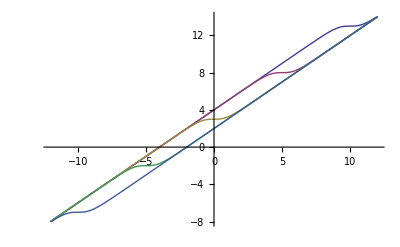

```mathematica
Plot[{fg3[x]/.c->-10,fg3[x]/.c->-5,fg3[x]/.c->0,fg3[x]/.c->5,fg3[x]/.c->10,},{x,-12,12}]
```

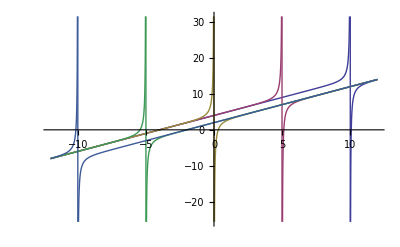

```mathematica
Plot[{fg4[x]/.c->-10,fg4[x]/.c->-5,fg4[x]/.c->0,fg4[x]/.c->5,fg4[x]/.c->10,},{x,-12,12}]
```

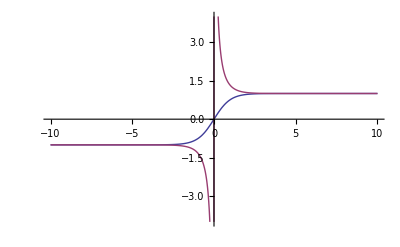

```mathematica
Plot[{Tanh[x],Coth[x]},{x,-10,10}]
```

### (i) y=x y'-√(x^2+y^2)

The solution is y=(c x^2-1/c)/2; c>0

Solve for y'=(√(x^2+y^2)+y)/x

```mathematica
fi1[x_,y_]:=(Sqrt[x^2+y^2]+y)/x
```

```mathematica
fi1[x,y]//TraditionalForm
```

(√(x^2+y^2)+y)/x

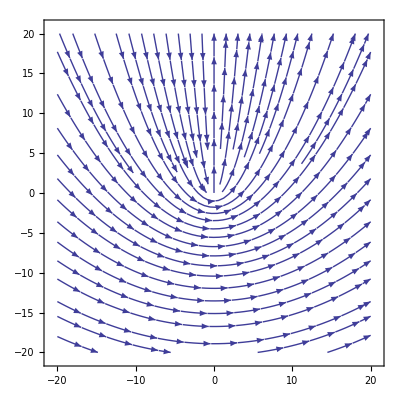

```mathematica
StreamPlot[{1,fi1[x,y]},{x,-20,20},{y,-20,20}]
```

Let u=y/x. Then y'=u+xu'and dividing (i) by x we get u=-√(1+u^2)+u+xu' and  ⅆu/(√(1+u^2))=ⅆx/x
sinh^-1(u)=c+log(x) and u=sinh(c+log(x)) and y=x sinh(c+log(x)) = 1/2 (a x^2-1/a); a=ⅇ^c>0

```mathematica
fi2[x_]:=(c*x^2 - 1/c)/2
```

```mathematica
fi2[x]//TraditionalForm
```

1/2 (c x^2-1/c)

```mathematica
fi2'[x]
```

c x

```mathematica
FullSimplify[fi1[x,fi2[x]],{Element[x,Reals],c>0}]
```

c x